```mathematica
paulis=PauliMatrix/@Range[3]
```

{{{0,1},{1,0}},{{0,-ⅈ},{ⅈ,0}},{{1,0},{0,-1}}}

```mathematica
c=FullSimplify[MatrixExp[-I*θ/2*({Sin[α]Cos[ϕ],Sin[α]Sin[ϕ],Cos[α]}.paulis)]]
```

{{Cos[θ/2]-ⅈ Cos[α] Sin[θ/2],Sin[α] Sin[θ/2] (-ⅈ Cos[ϕ]-Sin[ϕ])},{Sin[α] Sin[θ/2] (-ⅈ Cos[ϕ]+Sin[ϕ]),Cos[θ/2]+ⅈ Cos[α] Sin[θ/2]}}

```mathematica
ψ0={1,0}
```

{1,0}

```mathematica
c.ψ0
```

{Cos[θ/2]-ⅈ Cos[α] Sin[θ/2],Sin[α] Sin[θ/2] (-ⅈ Cos[ϕ]+Sin[ϕ])}

```mathematica
FullSimplify[(Cos[θ/2]-ⅈ Cos[α] Sin[θ/2])*(Cos[θ/2]+ⅈ Cos[α] Sin[θ/2])]
```

Cos[θ/2]^2+Cos[α]^2 Sin[θ/2]^2

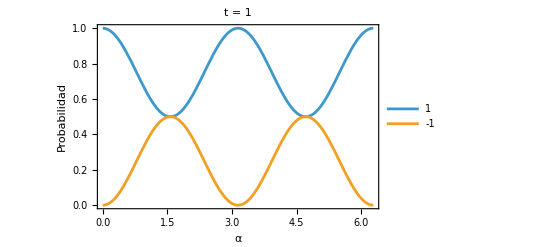

```mathematica
Plot[{FullSimplify[(Cos[θ/2]-ⅈ Cos[α] Sin[θ/2])*(Cos[θ/2]+ⅈ Cos[α] Sin[θ/2])]/.θ->Pi/2,FullSimplify[(Sin[α] Sin[θ/2] (-ⅈ Cos[ϕ]+Sin[ϕ]))(Sin[α] Sin[θ/2] (ⅈ Cos[ϕ]+Sin[ϕ]))]/.θ->Pi/2},{α,0,2Pi},
PlotLegends->{1,-1},
LabelStyle->Directive[Black,FontSize->18],
Frame->True,
FrameLabel->{α, "Probabilidad"},
FrameStyle->Directive[Black,FontSize->18],
PlotLabel->Style["t = 1",Black,FontSize->18]
]
```

### t=2

```mathematica
(*x=1*)
FullSimplify[c.{Cos[θ/2]-ⅈ Cos[α] Sin[θ/2],0}]
```

{(Cos[θ/2]-ⅈ Cos[α] Sin[θ/2])^2,Sin[α] Sin[θ/2] (Cos[θ/2]-ⅈ Cos[α] Sin[θ/2]) (-ⅈ Cos[ϕ]+Sin[ϕ])}

```mathematica
(*x=-1*)
FullSimplify[c.{0,-I Exp[I ϕ]Sin[α] Sin[θ/2]}]
```

{-Sin[α]^2 Sin[θ/2]^2,ⅇ^(ⅈ ϕ) Sin[α] Sin[θ/2] (-ⅈ Cos[θ/2]+Cos[α] Sin[θ/2])}

```mathematica
θ=Pi/2;
FullSimplify[(Cos[θ/2]-ⅈ Cos[α] Sin[θ/2])^2*(Cos[θ/2]+ⅈ Cos[α] Sin[θ/2])^2]
FullSimplify[((Sin[α] Sin[θ/2] (Cos[θ/2]-ⅈ Cos[α] Sin[θ/2]) (-ⅈ Cos[ϕ]+Sin[ϕ]))(Sin[α] Sin[θ/2] (Cos[θ/2]+ⅈ Cos[α] Sin[θ/2]) (+ⅈ Cos[ϕ]+Sin[ϕ]))+(-Sin[α]^2 Sin[θ/2]^2)(-Sin[α]^2 Sin[θ/2]^2))]
FullSimplify[(ⅇ^(ⅈ ϕ) Sin[α] Sin[θ/2] (-ⅈ Cos[θ/2]+Cos[α] Sin[θ/2]))(ⅇ^(-ⅈ ϕ) Sin[α] Sin[θ/2] (+ⅈ Cos[θ/2]+Cos[α] Sin[θ/2]))]
```

1/16 (3+Cos[2 α])^2

Sin[α]^2/2

1/8 (3+Cos[2 α]) Sin[α]^2

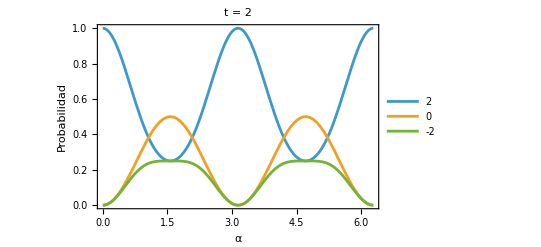

```mathematica
Plot[{1/16 (3+Cos[2 α])^2,Sin[α]^2/2,1/8 (3+Cos[2 α]) Sin[α]^2},{α,0,2Pi},
PlotLegends->{2,0,-2},
LabelStyle->Directive[Black,FontSize->18],
Frame->True,
FrameLabel->{α, "Probabilidad"},
FrameStyle->Directive[Black,FontSize->18],
PlotLabel->Style["t = 2",Black,FontSize->18]
]
```